### Start choosing the example:

```mathematica
t=22;
beta =0;
A = 0.2;
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1}},Switching Costs→{{1,2,3,S1},{3,2,1,S2}}|>

```mathematica
Data["Switching Costs"]={}
```

{}

```mathematica
MFGEquations=DataToEquations[Data/.{I1-> 80, U1-> 15}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 2.×10^-6 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.008073,Null}

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j481→80.,j482→80.,j483→80.,j484→80.,j485→0.,j486→0.,j487→0.,j488→0.,jt489→0.,jt490→80.,jt491→80.,jt492→0.,jt493→80.,jt494→0.,u495→175.,u496→95.,u497→15.,u498→175.,u499→95.,u500→15.,u501→15.,u502→175.|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=Catch @ FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.62246×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.62246×10^-17

<|j481→80,j482→80,j483→80,j484→80,j485→0.,j486→0.,j487→0.,j488→0.,jt489→0.,jt490→80,jt491→80,jt492→0.,jt493→80,jt494→0.,u495→20.1639,u496→17.582,u497→15.,u498→20.1639,u499→17.582,u500→15.,u501→15.,u502→20.1639|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 6.53876×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 6.53876×10^-17

<|j481→80,j482→80,j483→80,j484→80,j485→0.,j486→0.,j487→0.,j488→0.,jt489→0.,jt490→80,jt491→80,jt492→0.,jt493→80,jt494→0.,u495→21.3227,u496→18.1613,u497→15.,u498→21.3227,u499→18.1613,u500→15.,u501→15.,u502→21.3227|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00518×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00518×10^-16

<|j481→80,j482→80,j483→80,j484→80,j485→0.,j486→0.,j487→0.,j488→0.,jt489→0.,jt490→80,jt491→80,jt492→0.,jt493→80,jt494→0.,u495→25.0478,u496→20.0239,u497→15.,u498→25.0478,u499→20.0239,u500→15.,u501→15.,u502→25.0478|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j481→80,j482→80,j483→80,j484→80,j485→0.,j486→0.,j487→0.,j488→0.,jt489→0.,jt490→80,jt491→80,jt492→0.,jt493→80,jt494→0.,u495→104.932,u496→59.966,u497→15.,u498→104.932,u499→59.966,u500→15.,u501→15.,u502→104.932|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.20583×10^-13

<|j481→80,j482→80,j483→80,j484→80,j485→0.,j486→0.,j487→0.,j488→0.,jt489→0.,jt490→80,jt491→80,jt492→0.,jt493→80,jt494→0.,u495→175.,u496→95.,u497→15.,u498→175.,u499→95.,u500→15.,u501→15.,u502→175.|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j481→80,j482→80,j483→80,j484→80,j485→0.,j486→0.,j487→0.,j488→0.,jt489→0.,jt490→80,jt491→80,jt492→0.,jt493→80,jt494→0.,u495→742.811,u496→378.906,u497→15.,u498→742.811,u499→378.906,u500→15.,u501→15.,u502→742.811|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j481→80,j482→80,j483→80,j484→80,j485→0.,j486→0.,j487→0.,j488→0.,jt489→0.,jt490→80,jt491→80,jt492→0.,jt493→80,jt494→0.,u495→45695.9,u496→22855.5,u497→15.,u498→45695.9,u499→22855.5,u500→15.,u501→15.,u502→45695.9|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j481→80,j482→80,j483→80,j484→80,j485→0.,j486→0.,j487→0.,j488→0.,jt489→0.,jt490→80,jt491→80,jt492→0.,jt493→80,jt494→0.,u495→580101.,u496→290058.,u497→15.,u498→580101.,u499→290058.,u500→15.,u501→15.,u502→580101.|>

```mathematica
alpha = 1.6001;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],200,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j481→80,j482→80,j483→80,j484→80,j485→0.,j486→0.,j487→0.,j488→0.,jt489→0.,jt490→80,jt491→80,jt492→0.,jt493→80,jt494→0.,u495→581900.,u496→290958.,u497→15.,u498→581900.,u499→290958.,u500→15.,u501→15.,u502→581900.|>

```mathematica
alpha = 1.605;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j481→80,j482→80,j483→80,j484→80,j485→0.,j486→0.,j487→0.,j488→0.,jt489→0.,jt490→80,jt491→80,jt492→0.,jt493→80,jt494→0.,u495→678389.,u496→339202.,u497→15.,u498→678389.,u499→339202.,u500→15.,u501→15.,u502→678389.|>

```mathematica
alpha = 1.61;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j481→80,j482→80,j483→80,j484→80,j485→0.,j486→0.,j487→0.,j488→0.,jt489→0.,jt490→80,jt491→80,jt492→0.,jt493→80,jt494→0.,u495→796137.,u496→398076.,u497→15.,u498→796137.,u499→398076.,u500→15.,u501→15.,u502→796137.|>

```mathematica
alpha = 1.62;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j481→80,j482→80,j483→80,j484→80,j485→0.,j486→0.,j487→0.,j488→0.,jt489→0.,jt490→80,jt491→80,jt492→0.,jt493→80,jt494→0.,u495→1.10875×10^6,u496→554381.,u497→15.,u498→1.10875×10^6,u499→554381.,u500→15.,u501→15.,u502→1.10875×10^6|>

```mathematica
alpha = 1.65;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j481→80,j482→80,j483→80,j484→80,j485→0.,j486→0.,j487→0.,j488→0.,jt489→0.,jt490→80,jt491→80,jt492→0.,jt493→80,jt494→0.,u495→3.30779×10^6,u496→1.6539×10^6,u497→15.,u498→3.30779×10^6,u499→1.6539×10^6,u500→15.,u501→15.,u502→3.30779×10^6|>

```mathematica
alpha = 1.7;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j481→80,j482→80,j483→80,j484→80,j485→0.,j486→0.,j487→0.,j488→0.,jt489→0.,jt490→80,jt491→80,jt492→0.,jt493→80,jt494→0.,u495→3.119×10^7,u496→1.5595×10^7,u497→15.,u498→3.119×10^7,u499→1.5595×10^7,u500→15.,u501→15.,u502→3.119×10^7|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j481→80,j482→80,j483→80,j484→80,j485→0.,j486→0.,j487→0.,j488→0.,jt489→0.,jt490→80,jt491→80,jt492→0.,jt493→80,jt494→0.,u495→4.81052×10^10,u496→2.40526×10^10,u497→15.,u498→4.81052×10^10,u499→2.40526×10^10,u500→15.,u501→15.,u502→4.81052×10^10|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j481→80,j482→80,j483→80,j484→80,j485→0.,j486→0.,j487→0.,j488→0.,jt489→0.,jt490→80,jt491→80,jt492→0.,jt493→80,jt494→0.,u495→1.12074×10^19,u496→5.6037×10^18,u497→15.,u498→1.12074×10^19,u499→5.6037×10^18,u500→15.,u501→15.,u502→1.12074×10^19|>

```mathematica
alpha = 1.99;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j481→80,j482→80,j483→80,j484→80,j485→0.,j486→0.,j487→0.,j488→0.,jt489→0.,jt490→80,jt491→80,jt492→0.,jt493→80,jt494→0.,u495→3.98121×10^105,u496→1.99061×10^105,u497→15.,u498→3.98121×10^105,u499→1.99061×10^105,u500→15.,u501→15.,u502→3.98121×10^105|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j481→80,j482→80,j483→80,j484→80,j485→0.,j486→0.,j487→0.,j488→0.,jt489→0.,jt490→80,jt491→80,jt492→0.,jt493→80,jt494→0.,u495→4.4098×10^106,u496→2.2049×10^106,u497→15.,u498→4.4098×10^106,u499→2.2049×10^106,u500→15.,u501→15.,u502→4.4098×10^106|>

### What we this plot for?

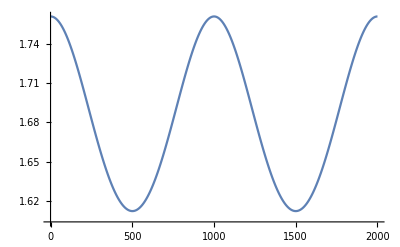

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.